```mathematica
GContract[g_,e_]:=If[EdgeQ[g,e],EdgeContract[g,e],VertexContract[g,{e[[1]],e[[2]]}]]
```

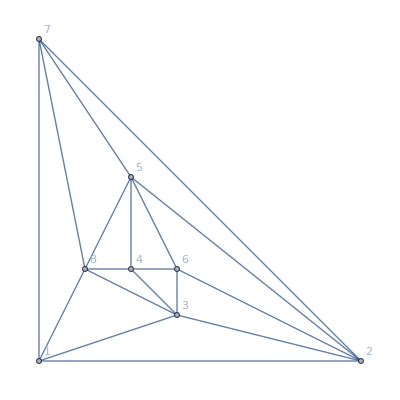
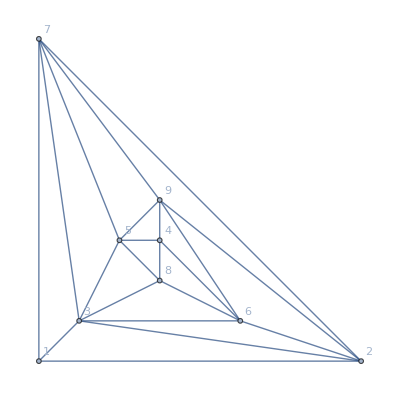
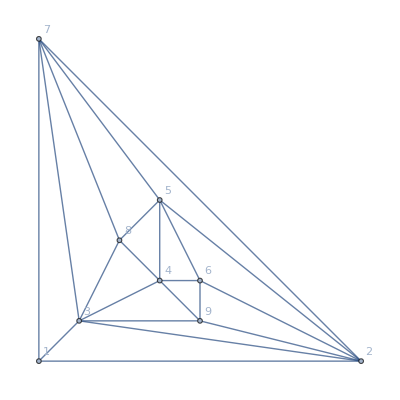
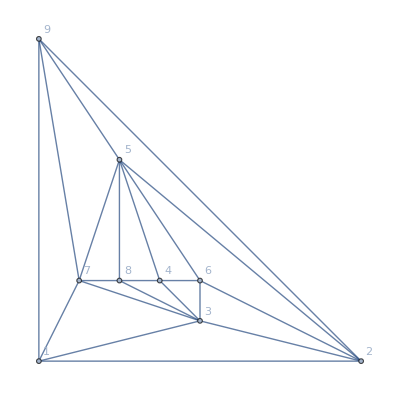
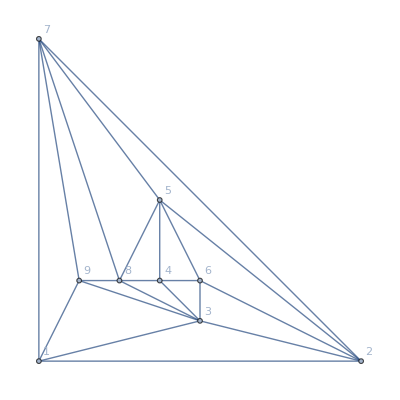
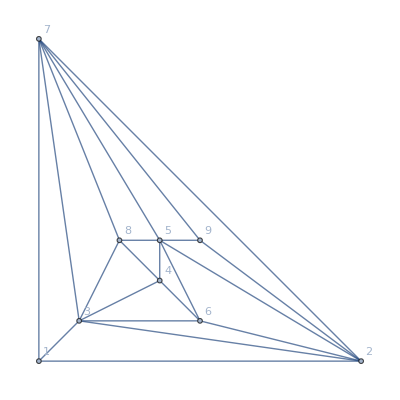
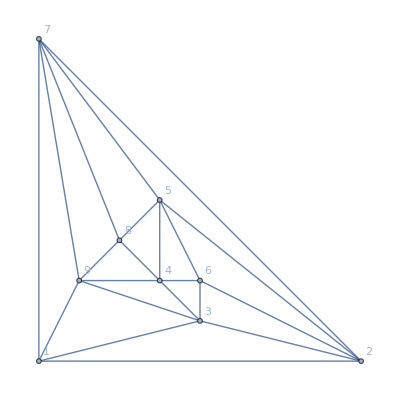
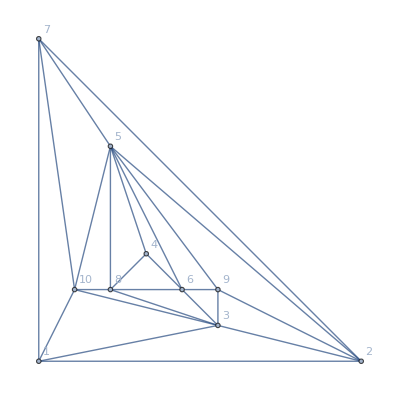
{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,-Graphics-{3,18},Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,-Graphics-{3,36},Null,-Graphics-{3,38},Null,-Graphics-{9,40},-Graphics-{6,41},Null,Null,Null,-Graphics-{5,45},-Graphics-{2,46},Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,-Graphics-{9,91},Null,Null,-Graphics-{3,94},Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,-Graphics-{6,107},-Graphics-{2,108},-Graphics-{3,109},Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,-Graphics-{13,120},-Graphics-{9,121},-Graphics-{2,122},Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,-Graphics-{6,146},Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,-Graphics-{3,159},Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,-Graphics-{6,170},-Graphics-{14,171},-Graphics-{3,172},Null,Null,-Graphics-{5,175},Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,-Graphics-{3,187},-Graphics-{3,188},Null,Null,Null,Null,Null,Null,Null,-Graphics-{3,196},-Graphics-{3,197},Null,Null,Null,Null,-Graphics-{8,202},Null,Null,-Graphics-{11,205},-Graphics-{9,206},-Graphics-{7,207},-Graphics-{9,208},Null,-Graphics-{12,210},Null,Null,Null,-Graphics-{6,214},-Graphics-{5,215},-Graphics-{2,216},Null,-Graphics-{14,218},-Graphics-{6,219},-Graphics-{3,220},-Graphics-{3,221},-Graphics-{3,222},-Graphics-{3,223},-Graphics-{6,224},Null,Null,Null,Null,Null,Null,Null,Null,-Graphics-{28,233},Null,-Graphics-{5,235},Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,-Graphics-{4,298},-Graphics-{4,299},Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,-Graphics-{9,340},Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,-Graphics-{7,378},Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,-Graphics-{13,403},Null,-Graphics-{11,405},Null,-Graphics-{7,407},-Graphics-{5,408},Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,-Graphics-{9,437},Null,Null,Null,Null,-Graphics-{11,442},Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,-Graphics-{7,457},-Graphics-{10,458},Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,-Graphics-{14,478},-Graphics-{6,479},Null,Null,-Graphics-{6,482},Null,Null,-Graphics-{9,485},-Graphics-{12,486},Null,Null,-Graphics-{5,489},-Graphics-{6,490},Null,Null,Null,Null,Null,Null,Null,Null,Null,-Graphics-{11,500}}

```mathematica
Table[With[{g=ReadGrof[k]},If[!Fold[Or,Table[PlanarGraphQ[GContract[g,e]],{e,EdgeList[GraphComplement[g]]}]],Labeled[Graph[g,GraphLayout->"PlanarEmbedding",VertexLabels->"Name"],{ChromaticPolynomial[g,4]/24,k}],Null]],{k,2,500}]
```

```mathematica
With[{g=ReadGrof[46]},Table[PlanarGraphQ[VertexContract[g,{e[[1]],e[[2]]}]],{e,EdgeList[GraphComplement[g]]}]]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

```mathematica
Monitor[Table[With[{g=ReadGrof[k]},If[!Fold[Or,Table[MaximalPlanarQ[EdgeContract[g,e]],{e,EdgeList[g]}]],Labeled[Graph[g,GraphLayout->"PlanarEmbedding",VertexLabels->"Name"],{ChromaticPolynomial[g,4]/24,k}],Null]],{k,2,1000}],k]
```

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

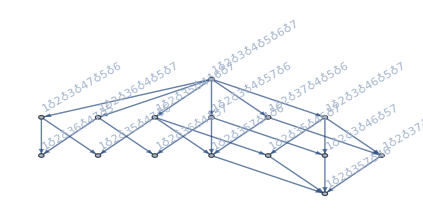
{-Graphics-,{v1x2x3x4x6x7,v1x2x37x4x6,v1x2x3x47x6,v1x2x3x46x7,v1x2x37x46,v1x2x3x4x5x7,v1x2x3x4x57,v1x2x3x47x5,v1x2x3x4x5x6,v1x2x35x4x6,v1x2x3x46x5,v1x2x35x46,v1x2x3x4x5x7,v1x2x3x4x57,v1x2x37x4x5,v1x2x35x4x7,v1x2x357x4,v1x2x3x4x5x6,v1x2x36x4x5,v1x2x35x4x6,v1x2x3x4x5x6,v1x2x3x46x5,v1x2x35x4x6,v1x2x35x46,v1x2x36x4x5}}

```mathematica
With[{g=MinimalGraph[6]},
With[{full=FindFullFormula[g]},
{FormulaGraphReverse2[full],
Flatten[Table[FindFullFormula[GContract[g,e]],{e,EdgeList[GraphComplement[g]]}]]
}
]
]
```

```mathematica
DrawNormal[form_]:=Block[{labels=Map[#[[1]]->Rotate[Labeled[SymbolToLabel[#[[1]]],Style[#[[2]],Red]],Pi/6]&,Tally[form]]},
Graph[FormulaGraphReverse2[form],VertexLabels->labels,ImageSize->650]
]
```

```mathematica
EdgeList[GraphComplement[MinimalGraph[6]]]
```

{3<->5,3<->6,3<->7,4<->6,4<->7,5<->7}

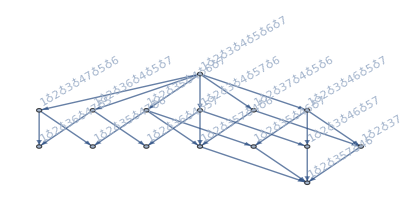
{-Graphics-,{v1x2x3x4x6x7,v1x2x37x4x6,v1x2x3x47x6,v1x2x3x46x7,v1x2x37x46,v1x2x3x4x5x7,v1x2x3x4x57,v1x2x3x47x5,v1x2x3x4x5x6,v1x2x35x4x6,v1x2x3x46x5,v1x2x35x46,v1x2x3x4x5x7,v1x2x3x4x57,v1x2x37x4x5,v1x2x35x4x7,v1x2x357x4,v1x2x3x4x5x6,v1x2x36x4x5,v1x2x35x4x6,v1x2x3x4x5x6,v1x2x3x46x5,v1x2x35x4x6,v1x2x35x46,v1x2x36x4x5}}

```mathematica
With[{g=MinimalGraph[6]},
With[{full=FindFullFormula[g]},
{FormulaGraphReverse2[full],
Flatten[Table[FindFullFormula[GContract[g,e]],{e,EdgeList[GraphComplement[g]]}]]
}
]
]
```

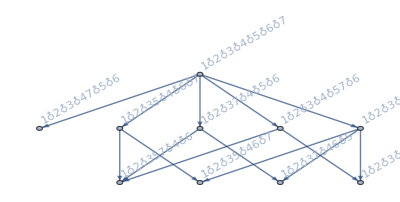
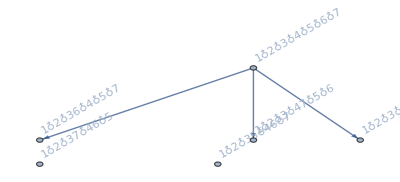
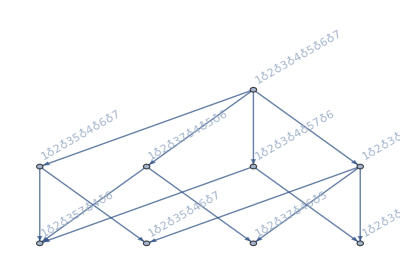
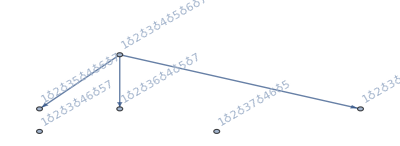
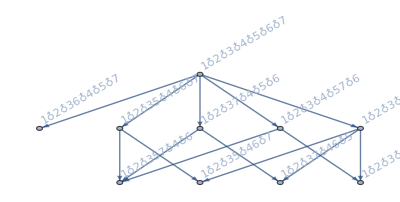
{-Graphics-,{v1x2x357x4x6,v1x2x35x46x7,v1x2x37x46x5,v1x2x3x46x57},{v1x2x357x46},{-Graphics-3<->5,-Graphics-3<->6,-Graphics-3<->7,-Graphics-4<->6,-Graphics-4<->7,-Graphics-5<->7}}

```mathematica
With[{g=MinimalGraph[6]},
With[{full=FindFullFormula[g]},
{FormulaGraphReverse2[full],
AlmostSinks[FormulaGraphReverse2[full]],
Sinks[FormulaGraphReverse[full]],
Table[Labeled[FormulaGraphReverse2[AugmentedFormula[FindFullFormula[EdgeContract[g,e]],e,full]],e],{e,EdgeList[GraphComplement[g]]}]
}
]
]
```

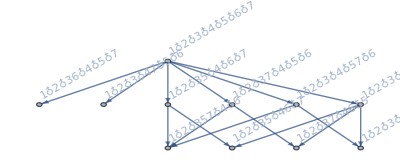
{-Graphics-,{v1x2x357x4x6,v1x2x35x46x7,v1x2x37x46x5,v1x2x3x46x57},{v1x2x357x46},-Graphics-}

```mathematica
With[{g=MinimalGraph[6]},
With[{full=FindFullFormula[g]},
{Graph[FormulaGraphReverse2[full],GraphHighlight->EdgeList[FormulaGraphReverse2[Flatten[Table[AugmentedFormula[FindFullFormula[GContract[g,e]],e,full],{e,EdgeList[GraphComplement[g]]}]]]],
GraphHighlightStyle->"Thick",
ImageSize->600],
AlmostSinks[FormulaGraphReverse2[full]],
Sinks[FormulaGraphReverse[full]],
FormulaGraphReverse2[Flatten[Table[AugmentedFormula[FindFullFormula[GContract[g,e]],e,full],{e,EdgeList[GraphComplement[g]]}]]]
}
]
]
```

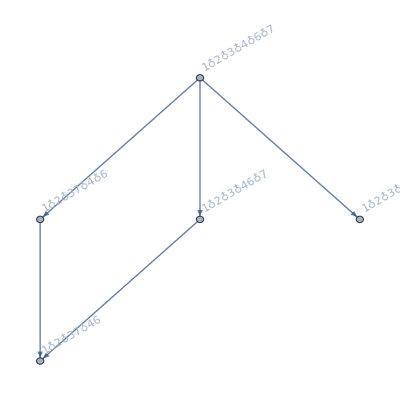
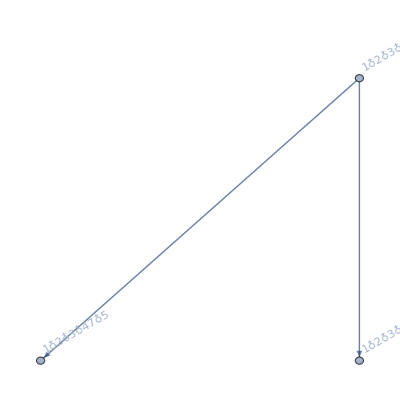
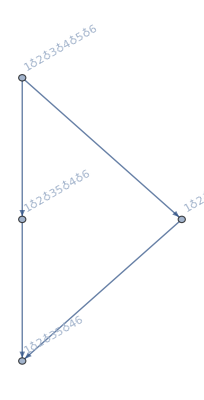
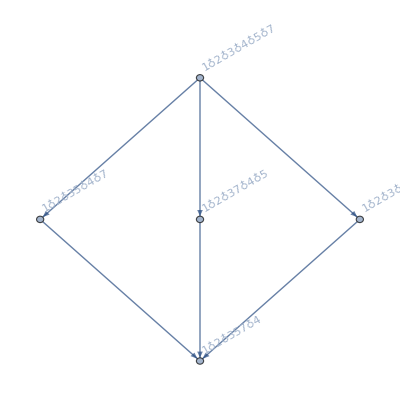
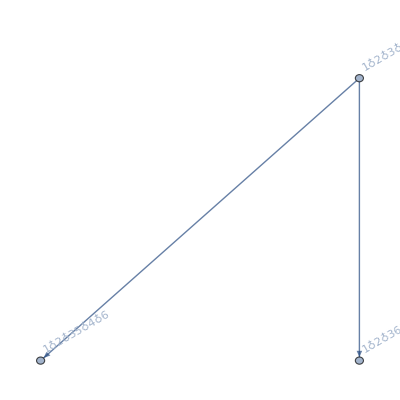
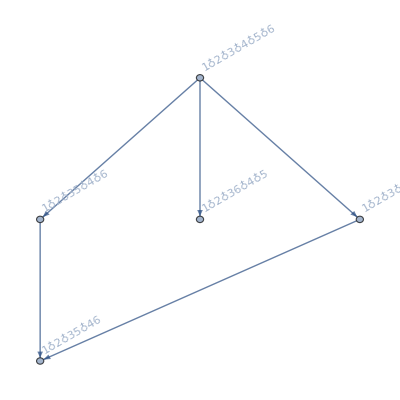
{-Graphics-,{v1x2x357x4x6,v1x2x35x46x7,v1x2x37x46x5,v1x2x3x46x57},{v1x2x357x46},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
With[{g=MinimalGraph[6]},
With[{full=FindFullFormula[g]},
{FormulaGraphReverse2[full],
AlmostSinks[FormulaGraphReverse2[full]],
Sinks[FormulaGraphReverse[full]],
Table[FormulaGraphReverse2[FindFullFormula[GContract[g,e]]],{e,EdgeList[GraphComplement[g]]}]
}
]
]
```

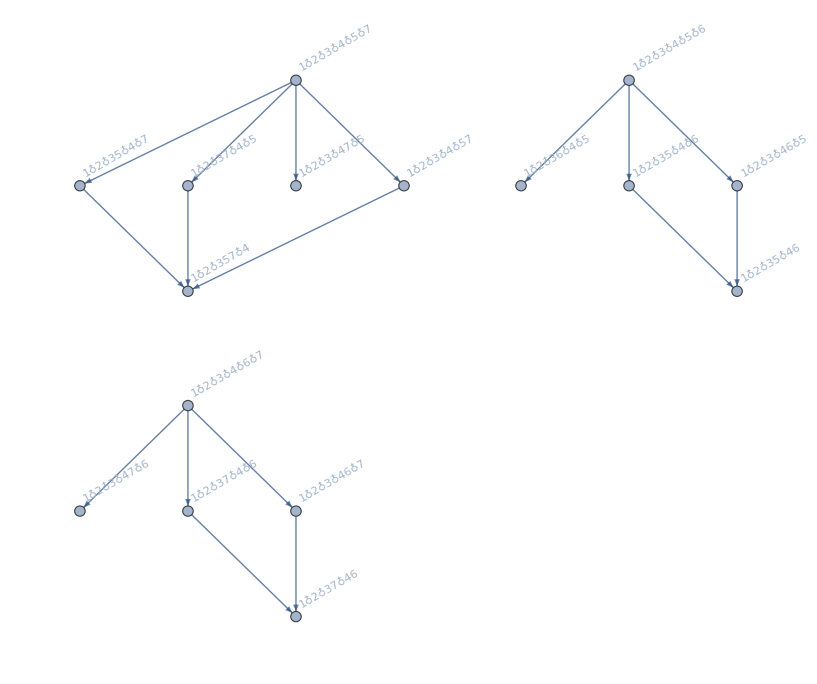
{-Graphics-,-Graphics-}

```mathematica
With[{g=MinimalGraph[6]},
With[{full=FindFullFormula[g]},
{FormulaGraphReverse2[full],
Graph[FormulaGraphReverse2[Flatten[Table[FindFullFormula[GContract[g,e]],{e,EdgeList[GraphComplement[g]]}]]]]
}
]
]
```

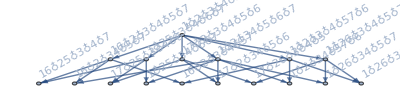
{-Graphics-,{v16x25x3x4x7,v16x2x34x5x7,v1x25x34x6x7,v16x2x3x4x57,v1x2x34x57x6,v17x25x3x4x6,v17x2x34x5x6,v17x26x3x4x5,v1x26x34x5x7,v1x26x3x4x57},{v16x25x34x7,v16x2x34x57,v17x25x34x6,v17x26x34x5,v1x26x34x57},-Graphics-}

```mathematica
With[{g=JacobsThalGraph[3]},
With[{full=FindFullFormula[g]},
{Graph[FormulaGraphReverse2[full],GraphHighlight->EdgeList[FormulaGraphReverse2[Flatten[Table[AugmentedFormula[FindFullFormula[GContract[g,e]],e,full],{e,EdgeList[GraphComplement[g]]}]]]],
GraphHighlightStyle->"Thick",
ImageSize->600],
AlmostSinks[FormulaGraphReverse2[full]],
Sinks[FormulaGraphReverse[full]],
FormulaGraphReverse2[Flatten[Table[AugmentedFormula[FindFullFormula[GContract[g,e]],e,full],{e,EdgeList[GraphComplement[g]]}]]]
}
]
]
```

```mathematica
Table[
With[{g=ReadGrof[k]},
With[{full=FindFullFormula[g]},
Labeled[
Graph[FormulaGraphReverse2[full],GraphHighlight->EdgeList[FormulaGraphReverse2[Flatten[Table[AugmentedFormula[FindFullFormula[GContract[g,e]],e,full],{e,EdgeList[GraphComplement[g]]}]]]],
GraphHighlightStyle->"Thick",
ImageSize->600,
VertexStyle->Table[v->Red,{v,AlmostSinks[FormulaGraphReverse2[full]]}]],
Style[k,20,Bold]]
]
],
{k,3,10}
]
```

{-Graphics-3,-Graphics-4,-Graphics-5,-Graphics-6,-Graphics-7,-Graphics-8,-Graphics-9,-Graphics-10}